# Curves and Surfaces for CAD systems

# -Graphics-

## Curve for Design

## 1) Parametric Curve and its properties

```mathematica
ClearAll["Global`*"]
x1= θ;
y1= Sin [θ];
MyCurve[θ_]={x1,y1};
UnitTangent[θ_]:={1/(√(1+Cos[θ]^2)),Cos[θ]/(√(1+Cos[θ]^2))}
UnitNormal[θ_]:={-Cos[θ]/(√(1+Cos[θ]^2)),1/(√(1+Cos[θ]^2))}
UnitTangentDeri1[θ_]:={√(1+Cos[θ]^2) Cot[θ] √(Sin[θ]^2/((1+Cos[θ]^2)^2)),-√(1+Cos[θ]^2) Csc[θ] √(Sin[θ]^2/((1+Cos[θ]^2)^2))};
CurveElp[θ_]:=-Sin[θ]/((1+Cos[θ]^2)^(3/2))
Quiet[Manipulate[
Show[
{ParametricPlot[MyCurve[θ],{θ, -π, π},PlotRange-> All],
Graphics[{Red,Arrow[{MyCurve[a],MyCurve[a]+UnitTangent[a]}]}],
Graphics[{Black,Arrow[{MyCurve[a],MyCurve[a]+UnitNormal[a]}]}],
Graphics[{Green,Arrow[{MyCurve[a],MyCurve[a]+UnitTangentDeri1[a]}]}],
Graphics[Circle[MyCurve[a]+(UnitTangentDeri1[a])*Abs[1/CurveElp[a]],Abs[1/CurveElp[a]]]],
Graphics[Point[MyCurve[a]+(UnitTangentDeri1[a])*Abs[1/CurveElp[a]]]],
Graphics[Point[MyCurve[a]]]}],{{a,-1.8},-π+0.1,π-0.1}]]
```

## 1) Extra: Curve Synthesis

```mathematica
intrinsic[fun_,a_:0,{c_0,d_:0,theta0_:0}, optsnd___,{smin_,smax_}][t_]:=Flatten[Module[{x,y,theta}, {x[t],y[t]}/.NDSolve[{x'[ss]==Cos[theta[ss]],y'[ss]==Sin[theta[ss]],theta'[ss]=fun[ss],x[a]==c,y[a]==d,theta[a]==theta0},{x,y,theta},{ss,smin,smax},optsnd]]]
plotintrinsic[fun_,a_:0,{c_:0,d_:0,theta0_:0},optsnd___,{smin_,smax_},optspp___]:=ParametricPlot[Module[{x,y,theta},{x[t],y[t]}/.NDSolve[{x'[ss]==Cos[theta[ss]],y'[ss]==Sin[theta[ss]],theta'[ss]==fun[ss],x[a]==c,y[a]==d, theta[a]==theta0},{x,y,theta},{ss,smin,smax},optsnd,MaxSteps->1000]]//Evaluate,{t,smin,smax},PlotRange->All,AspectRatio->Automatic, PlotStyle->Directive[Black,Thick] ,optspp];
```

### Curvature for case [s] = a s

```mathematica
Quiet[Manipulate[{plotintrinsic[#*a&,0,{0,0,0},{-5,5},PlotPoints->80],Plot[ s*a,{s,-5,5}, PlotRange->All]},{a,-10,10}]]
```

### Curvature for case [s] = a*Sin[s]

```mathematica
Quiet[Manipulate[{plotintrinsic[Sin[#]*a&,0,{0,0,0},{-5,5},PlotPoints->80],Plot[ Sin[s]*a,{s,-5,5}, PlotRange->All]},{a,-10,10}]]
```

## Bezier Curves

## 1) Linear Bezier

### Define the linear Bezier equation.

```mathematica
B1[t_, P0_,P1_]:=(1-t)P0+t *P1
```

### Draw a linear Bezier line connecting (0,0) and (2,1). Show the curve and it’s control points.

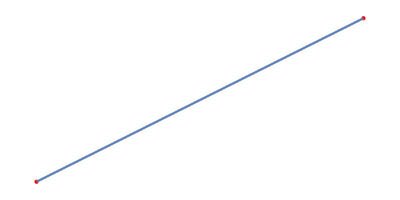

```mathematica
P1={p10,p11}={{0,0},{2,1}};
f11=ParametricPlot[B1[t,p10,p11],{t,0,1}];
f12=Graphics[{Red,PointSize[Large],Point[P1]}];
Show[f12,f11]
```

```mathematica
DynamicModule[
{P0={-2,-2},P1={2,2}},
LocatorPane[
Dynamic[{P0,P1}],
Dynamic[{
Show[{
ParametricPlot[(1-t)P0+t *P1,{t,0,1},PlotRange->{{-5,5},{-5,5}}, Axes->False, Frame->True],
ListPlot[{P0,P1},Joined-> True, PlotStyle->Red]
}],
Dynamic[{P0,P1}]}
]]]
```

## 2) Quadratic Bezier

### Define the quadratic Bezier equation.

```mathematica
B2[t_,p0_,p1_,p2_]:=p0 (1-t)^2+2t(1-t)p1+t^2 p2
basisFunction={b0[t_]= (1-t)^2,b1[t_]= 2t(1-t),b2[t_]= t^2};
```

### Basis Function plot

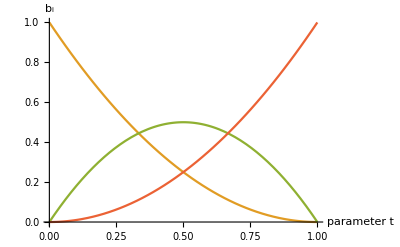

```mathematica
Plot[Evaluate[Table[basisFunction[[n]], {n,0,3}]], {t,0,1}, PlotRange->All,AxesLabel->{"parameter t","b_i" }]
```

### Draw a quadratic Bezier with control points (0,0), (2,3), and (4,-1). Draw the control points and polygons, then show the curve, control points and polygons in a single plot.

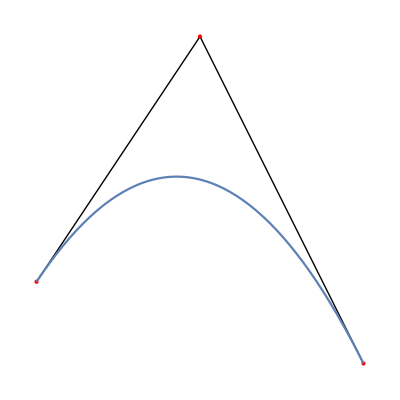

```mathematica
P2={p20,p21,p22}={{0,0},{2,3},{4,-1}};
f21=ParametricPlot[B2[t,p20,p21,p22],{t,0,1}];
f22=Graphics[{Line[P2],Red,PointSize[Large],Point[P2]}];
Show[f22,f21]
```

## 3) Interactive Bezier Cubic

```mathematica
DynamicModule[
{P0={0,0},P1={1,2},P2={3,0},P3={5,2}},
LocatorPane[
Dynamic[{P0,P1,P2,P3}],
Dynamic[{
Show[{
ParametricPlot[(1-t)^3 P0+3t (1-t)^2*P1+3 t^2 (1-t)*P2+t^3 P3,{t,0,1},PlotRange->{{-5,5},{-5,5}}, Axes->False, Frame->True],
ListPlot[{P0,P1,P2,P3},Joined-> True, PlotStyle->Red]
}],
Dynamic[{P0,P1,P2,P3}]}
]]]
```

## 4) de Casteljau Algo

```mathematica
ClearAll["Global`*"]
deCasteljau[t_, P0_,P1_]:=(1-t)P0+t P1
{p0,p1,p2,p3}={{0,0}, {1,2},{3,0},{5,2}};
Manipulate[Show[{ListPlot[{p0,p1,p2,p3},Joined-> True, PlotStyle->Red],
ListPlot[{p10=(1-t)p0+t p1,p11=(1-t)p1+t p2,p12=(1-t)p2+t p3}, PlotStyle->Black],
ListPlot[{p10,p11,p12}, Joined-> True, PlotStyle->Blue],
ListPlot[{p20=(1-t)p10+t p11,p21=(1-t)p11+t p12}, PlotStyle->Black],
ListPlot[{p20,p21}, Joined-> True, PlotStyle->Green],
ListPlot[{p30=(1-t)p20+t p21}, PlotStyle->Red],
ParametricPlot[{(1-t)^3 p0+3t (1-t)^2*p1+3 t^2 (1-t)*p2+t^3 p3}, {t,0,1}]
}, Frame->True, PlotRange->All],{t,0,1}]
```

## 5) Rational Bezier

```mathematica
ClearAll["Global`*"]
Bez[t_,w0_,w1_,w2_,w3_]:=(w0*(1-t)^3 P0 +w1*3t (1-t)^2 P1+w2*3 t^2(1-t)P2+ w3*t^3 P3)/(w0*(1-t)^3+w1*3t (1-t)^2+w2*3 t^2(1-t)+w3*t^3)
{P0,P1,P2,P3}={{0,3},{1,0},{5,5},{5,0}};
Bez[t,w0,w1,w2,w3]
Manipulate[Show[{ParametricPlot[Bez[t,w0,w1,w2,w3],{t,0,1}],ListPlot[{{P0,P1,P2,P3}},Joined->True, PlotStyle->Gray],ListPlot[{{P0,P1,P2,P3}},PlotStyle->Red],Graphics[{Text[Subscript[P, 0],P0-0.2]}]},PlotRange->{{-1,6},{-1,6}},AxesOrigin->{0,0}],{w0,0.1,1},{w1,0.1,1},{w2,0.1,1},{w3,0.1,1}]
```

{(3 (1-t)^2 t w1+15 (1-t) t^2 w2+5 t^3 w3)/((1-t)^3 w0+3 (1-t)^2 t w1+3 (1-t) t^2 w2+t^3 w3),(3 (1-t)^3 w0+15 (1-t) t^2 w2)/((1-t)^3 w0+3 (1-t)^2 t w1+3 (1-t) t^2 w2+t^3 w3)}

## 6) General Bezier: basis functions

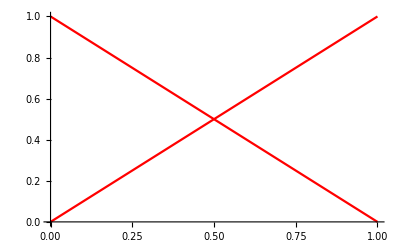
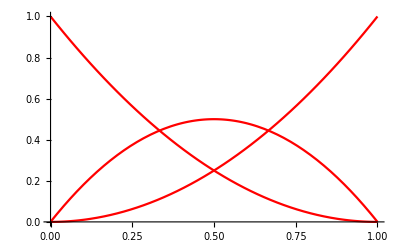
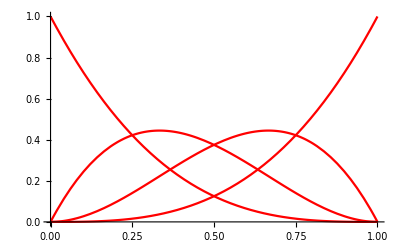
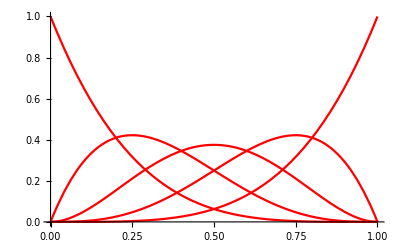
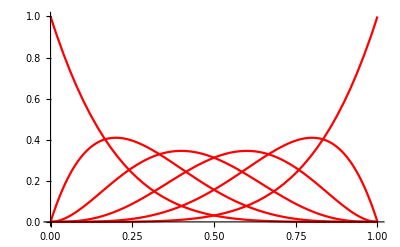
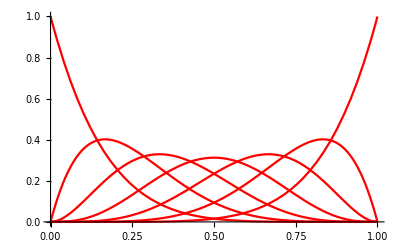
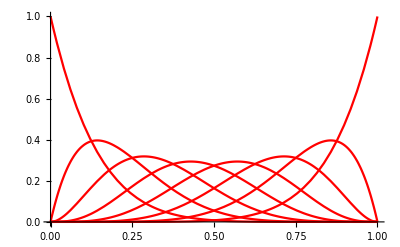
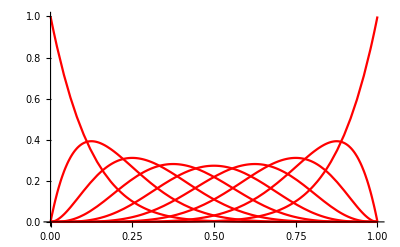

```mathematica
Table[Plot[Evaluate[Table[BernsteinBasis[m,n,t],{n,0,m}]],{t,0,1}, PlotStyle->Red, PlotRange->All],{m,1,9}]
```

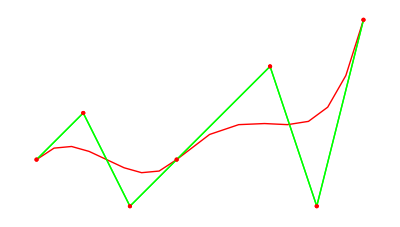

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{5,2},{6,-1},{7,3}};
Pygn=Graphics[{Green,Line[pts],Red,Point[pts]}];
BezStandard=Graphics[{Red,BezierCurve[pts,SplineDegree->7],Green,Line[pts],Red,Point[pts]}];

Show[Pygn,BezStandard, PlotRange->All]
```

## 7) Application: Font Design / Morphing

Define the outline of a glyph:

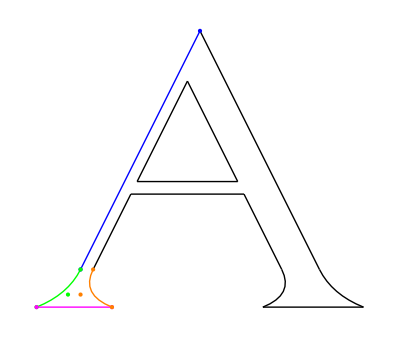

```mathematica
curves=Graphics[{
Blue,BezierCurve[pts1={{2,3},{0.8125,0.625}}],
Green,BezierCurve[pts2={{0.8125,0.625},{0.6875,0.375},{0.375,0.25}}],
Magenta,BezierCurve[pts3={{0.375,0.25},{1.125,0.25}}],
Orange,BezierCurve[pts4={{1.125,0.25},{0.8125,0.375},{0.9375,0.625}}],
Black,BezierCurve[{{0.9375,0.625},{1.3125,1.375}}],
BezierCurve[{{1.3125,1.375},{2.4375,1.375}}],
BezierCurve[{{2.4375,1.375},{2.8125,0.625}}],
BezierCurve[{{2.8125,0.625},{2.9375,0.375},{2.625,0.25}}],
BezierCurve[{{2.625,0.25},{3.625,0.25}}],
BezierCurve[{{3.625,0.25},{3.3125,0.375},{3.1875,0.625}}],
BezierCurve[{{3.1875,0.625},{2,3}}],
BezierCurve[{{1.875,2.5},{1.375,1.5}}],
BezierCurve[{{1.375,1.5},{2.375,1.5}}],
BezierCurve[{{2.375,1.5},{1.875,2.5}}]}];
points=Graphics[{Blue, Point[pts1], Green,Point[pts2], Magenta,Point[pts3],Orange,Point[pts4]}];
Show[{curves, points}]
```

Linear transition from one Bézier curve to another:

```mathematica
pts1={{0,-1},{2,1},{4,2},{6,2}};
pts2={{2,-1},{3,1},{4,-1},{6,0}};
g[p1_,p2_,t_]:=(1-t)p1+t p2
Animate[Graphics[{Blue,BezierCurve[pts1],Blue,BezierCurve[pts2],Thick,Red,BezierCurve[g[pts1,pts2,t]]}],{t,0,1},AnimationDirection->ForwardBackward,SaveDefinitions->True]
```

## 8) Cubic Bezier spline with G1 continuity

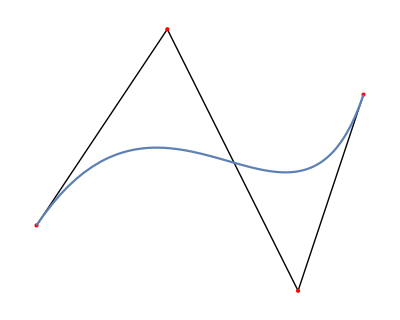

```mathematica
B3[t_,p0_,p1_,p2_,p3_]:=p0 (1-t)^3+3t(1-t)^2 p1+3 t^2(1-t)p2+t^3 p3
P3={p30,p31,p32,p33}={{0,0},{2,3},{4,-1},{5,2}};
P4={p40,p41,p42,p43}={{5,2},{5.3,2.9},{3,3},{3,1.5}};
f31=ParametricPlot[B3[t,p30,p31,p32,p33],{t,0,1}];
f32=Graphics[{Line[P3],Red,PointSize[Large],Point[P3]}];
Show[f32,f31]
```

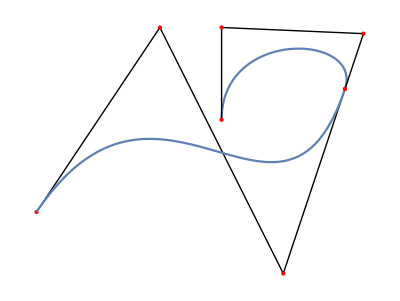

```mathematica
f42=Graphics[{Line[P4],Red,PointSize[Large],Point[P4]}];
f41=ParametricPlot[B3[t,p40,p41,p42,p43],{t,0,1}];
Show[f32,f31,f41,f42]
```

## BSplines

## 1) BSplines degree 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
d=2;
controlPoints={b0,b1,b2,b3};
m=(Dimensions[controlPoints][[1]]-1)+d+1
e=(m-d);
{Subscript[t, d],Subscript[t, e]}
```

6

{t_2,t_4}

```mathematica
knots={1,1,1,4,5,5,5};
b0={0,0};
b1={1,1};
b2={2,1};
b3={3,0};
td=knots[[d+1]];
tmd=knots[[m-d+1]];
Print[{Subscript[t, d],Subscript[t, e]},"=",{td,tmd}]
```

{t_2,t_4}={1,5}

```mathematica
k=0;
Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-1}]//TableForm
```

0{1,1,1,4,5,5,5}0x | 0
0{1,1,1,4,5,5,5}1x | 0
0{1,1,1,4,5,5,5}2x | = (Piecewise[{{1, 1≤x≤4}, {0, True}}])
0{1,1,1,4,5,5,5}3x | = (Piecewise[{{1, 4≤x≤5}, {0, True}}])
0{1,1,1,4,5,5,5}4x | 0
0{1,1,1,4,5,5,5}5x | 0

1{1,1,1,4,5,5,5}0x | 0
1{1,1,1,4,5,5,5}1x | = (Piecewise[{{(4-x)/3, 1≤x≤4}, {0, True}}])
1{1,1,1,4,5,5,5}2x | = (Piecewise[{{5-x, 4≤x≤5}, {1/3 (-1+x), 1≤x<4}, {0, True}}])
1{1,1,1,4,5,5,5}3x | = (Piecewise[{{-4+x, 4≤x≤5}, {0, True}}])
1{1,1,1,4,5,5,5}4x | 0

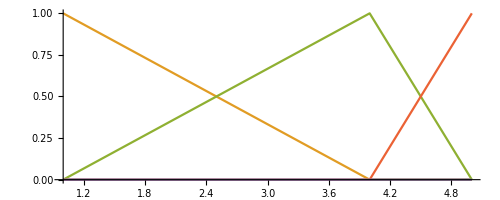

```mathematica
k=1;
Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-2}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-2}]],{x,1,5},AspectRatio-> Automatic, PlotRange->All]
```

{t_2,t_4}={1,5}

2{1,1,1,4,5,5,5}0x | = (Piecewise[{{1/9 (16-8 x+x^2), 1≤x≤4}, {0, True}}])
2{1,1,1,4,5,5,5}1x | = (Piecewise[{{1/36 (-31+38 x-7 x^2), 1≤x<4}, {1/4 (25-10 x+x^2), 4≤x≤5}, {0, True}}])
2{1,1,1,4,5,5,5}2x | = (Piecewise[{{1/4 (-85+42 x-5 x^2), 4≤x≤5}, {1/12 (1-2 x+x^2), 1≤x<4}, {0, True}}])
2{1,1,1,4,5,5,5}3x | = (Piecewise[{{16-8 x+x^2, 4≤x≤5}, {0, True}}])

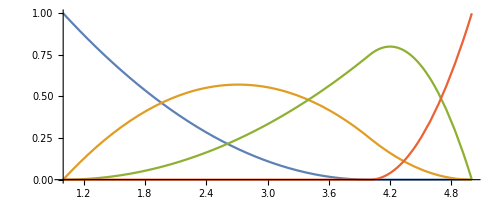

```mathematica
k=2;
Print[{Subscript[t, d],Subscript[t, e]},"=",{td,tmd}]
BSpline=Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-3}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-3}]],{x,1,5},AspectRatio-> Automatic,PlotRange->All]
```

```mathematica
Piece1=ParametricPlot[1/9 (16-8 x+x^2)b0+1/36 (-31+38 x-7 x^2)b1+1/12 (1-2 x+x^2)b2,{x,1,4},Frame->True,Axes->False,PlotRange->All,PlotStyle->Green];
```

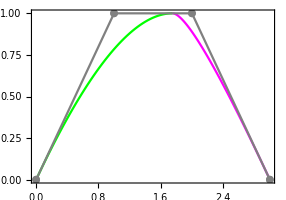

```mathematica
Piece2=ParametricPlot[1/4 (25-10 x+x^2)b1+1/4 (-85+42 x-5 x^2)b2+(16-8 x+x^2)b3,{x,4,5},Frame->True,Axes->False,PlotRange->All,PlotStyle->Magenta];
ctlpts=ListLinePlot[{b0,b1,b2,b3},Mesh->Full, PlotStyle->Gray];
Show[{Piece1,Piece2,ctlpts},AspectRatio-> Automatic]
```

## 2) BSplines degree 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
d=2;
controlPoints={b0,b1,b2,b3,b4};
m=(Dimensions[controlPoints][[1]]-1)+d+1
e=(m-d);
{Subscript[t, d],Subscript[t, e]}
```

7

{t_2,t_5}

```mathematica
knots={1,1,1,2,4,5,5,5};
b0={0,0};
b1={1,1};
b2={2,1};
b3={3,0};
b4={4,3};
td=knots[[d+1]];
tmd=knots[[m-d+1]];
Print[{Subscript[t, d],Subscript[t, e]},"=",{td,tmd}]
```

{t_2,t_5}={1,5}

```mathematica
k=0;
Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-1}]//TableForm
```

0{1,1,1,2,4,5,5,5}0x | 0
0{1,1,1,2,4,5,5,5}1x | 0
0{1,1,1,2,4,5,5,5}2x | = (Piecewise[{{1, 1≤x≤2}, {0, True}}])
0{1,1,1,2,4,5,5,5}3x | = (Piecewise[{{1, 2≤x≤4}, {0, True}}])
0{1,1,1,2,4,5,5,5}4x | = (Piecewise[{{1, 4≤x≤5}, {0, True}}])
0{1,1,1,2,4,5,5,5}5x | 0
0{1,1,1,2,4,5,5,5}6x | 0

1{1,1,1,2,4,5,5,5}0x | 0
1{1,1,1,2,4,5,5,5}1x | = (Piecewise[{{2-x, 1≤x≤2}, {0, True}}])
1{1,1,1,2,4,5,5,5}2x | = (Piecewise[{{(4-x)/2, 2≤x≤4}, {-1+x, 1≤x<2}, {0, True}}])
1{1,1,1,2,4,5,5,5}3x | = (Piecewise[{{5-x, 4≤x≤5}, {1/2 (-2+x), 2≤x<4}, {0, True}}])
1{1,1,1,2,4,5,5,5}4x | = (Piecewise[{{-4+x, 4≤x≤5}, {0, True}}])
1{1,1,1,2,4,5,5,5}5x | 0

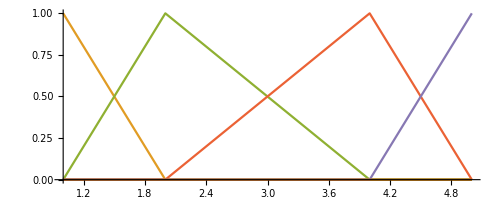

```mathematica
k=1;
Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-2}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-2}]],{x,1,5},AspectRatio-> Automatic, PlotRange->All]
```

{t_2,t_5}={1,5}

2{1,1,1,2,4,5,5,5}0x | = (Piecewise[{{4-4 x+x^2, 1≤x≤2}, {0, True}}])
2{1,1,1,2,4,5,5,5}1x | = (Piecewise[{{1/6 (16-8 x+x^2), 2≤x≤4}, {-2/3 (5-7 x+2 x^2), 1≤x<2}, {0, True}}])
2{1,1,1,2,4,5,5,5}2x | = (Piecewise[{{1/3 (-7+6 x-x^2), 2≤x<4}, {1/3 (25-10 x+x^2), 4≤x≤5}, {1/3 (1-2 x+x^2), 1≤x<2}, {0, True}}])
2{1,1,1,2,4,5,5,5}3x | = (Piecewise[{{1/6 (4-4 x+x^2), 2≤x<4}, {-2/3 (35-17 x+2 x^2), 4≤x≤5}, {0, True}}])
2{1,1,1,2,4,5,5,5}4x | = (Piecewise[{{16-8 x+x^2, 4≤x≤5}, {0, True}}])

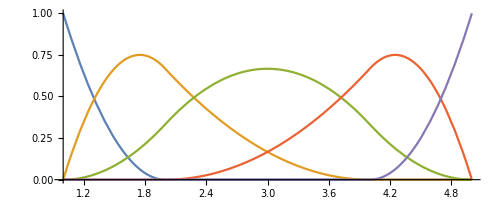

```mathematica
k=2;
Print[{Subscript[t, d],Subscript[t, e]},"=",{td,tmd}]
BSpline=Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-3}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-3}]],{x,1,5},AspectRatio-> Automatic,PlotRange->All]
```

```mathematica
Piece1=ParametricPlot[(4-4 x+x^2)b0-2/3 (5-7 x+2 x^2)b1+1/3 (1-2 x+x^2)b2,{x,1,2},Frame->True,Axes->False,PlotRange->All,PlotStyle->Green];

Piece2=ParametricPlot[1/6 (16-8 x+x^2)b1+1/3 (-7+6 x-x^2)b2+1/6 (4-4 x+x^2)b3,{x,2,4},Frame->True,Axes->False,PlotRange->All,PlotStyle->Red];

Piece3=ParametricPlot[1/3 (25-10 x+x^2)b2-2/3 (35-17 x+2 x^2)b3+(16-8 x+x^2)b4,{x,4,5},Frame->True,Axes->False,PlotRange->All,PlotStyle->Magenta];
```

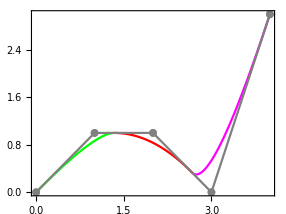

```mathematica
ctlpts=ListLinePlot[{b0,b1,b2,b3,b4},Mesh->Full, PlotStyle->Gray];
Show[{Piece1,Piece2,Piece3,ctlpts},AspectRatio-> Automatic]
```

## 3) BSplines degree 3

```mathematica
ClearAll["Global`*"]
```

```mathematica
d=3;
controlPoints={b0,b1,b2,b3,b4};
m=(Dimensions[controlPoints][[1]]-1)+d+1
e=(m-d);
{Subscript[t, d],Subscript[t, e]}
```

8

{t_3,t_5}

```mathematica
knots={1,1,1,1,3,4,5,6,7};
b0={0,0};
b1={1,1};
b2={2,1};
b3={3,0};
b4={4,3};
td=knots[[d+1]];
tmd=knots[[m-d+1]];
Print[{Subscript[t, d],Subscript[t, e]},"=",{td,tmd}]
```

{t_3,t_5}={1,4}

```mathematica
k=0;
Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-1}]//TableForm
```

0{1,1,1,1,3,4,5,6,7}0x | 0
0{1,1,1,1,3,4,5,6,7}1x | 0
0{1,1,1,1,3,4,5,6,7}2x | 0
0{1,1,1,1,3,4,5,6,7}3x | = (Piecewise[{{1, 1≤x≤3}, {0, True}}])
0{1,1,1,1,3,4,5,6,7}4x | = (Piecewise[{{1, 3≤x≤4}, {0, True}}])
0{1,1,1,1,3,4,5,6,7}5x | = (Piecewise[{{1, 4≤x≤5}, {0, True}}])
0{1,1,1,1,3,4,5,6,7}6x | = (Piecewise[{{1, 5≤x≤6}, {0, True}}])
0{1,1,1,1,3,4,5,6,7}7x | = (Piecewise[{{1, 6≤x≤7}, {0, True}}])

1{1,1,1,1,3,4,5,6,7}0x | 0
1{1,1,1,1,3,4,5,6,7}1x | 0
1{1,1,1,1,3,4,5,6,7}2x | = (Piecewise[{{(3-x)/2, 1≤x≤3}, {0, True}}])
1{1,1,1,1,3,4,5,6,7}3x | = (Piecewise[{{4-x, 3≤x≤4}, {1/2 (-1+x), 1≤x<3}, {0, True}}])
1{1,1,1,1,3,4,5,6,7}4x | = (Piecewise[{{5-x, 4≤x≤5}, {-3+x, 3≤x<4}, {0, True}}])
1{1,1,1,1,3,4,5,6,7}5x | = (Piecewise[{{6-x, 5≤x≤6}, {-4+x, 4≤x<5}, {0, True}}])
1{1,1,1,1,3,4,5,6,7}6x | = (Piecewise[{{7-x, 6≤x≤7}, {-5+x, 5≤x<6}, {0, True}}])

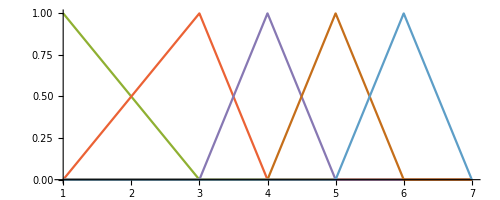

```mathematica
k=1;
Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-2}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-2}]],{x,1,7},AspectRatio-> Automatic, PlotRange->All]
```

2{1,1,1,1,3,4,5,6,7}0x | 0
2{1,1,1,1,3,4,5,6,7}1x | = (Piecewise[{{1/4 (9-6 x+x^2), 1≤x≤3}, {0, True}}])
2{1,1,1,1,3,4,5,6,7}2x | = (Piecewise[{{1/12 (-17+22 x-5 x^2), 1≤x<3}, {1/3 (16-8 x+x^2), 3≤x≤4}, {0, True}}])
2{1,1,1,1,3,4,5,6,7}3x | = (Piecewise[{{1/6 (-53+34 x-5 x^2), 3≤x<4}, {1/2 (25-10 x+x^2), 4≤x≤5}, {1/6 (1-2 x+x^2), 1≤x<3}, {0, True}}])
2{1,1,1,1,3,4,5,6,7}4x | = (Piecewise[{{1/2 (-39+18 x-2 x^2), 4≤x<5}, {1/2 (36-12 x+x^2), 5≤x≤6}, {1/2 (9-6 x+x^2), 3≤x<4}, {0, True}}])
2{1,1,1,1,3,4,5,6,7}5x | = (Piecewise[{{1/2 (-59+22 x-2 x^2), 5≤x<6}, {1/2 (49-14 x+x^2), 6≤x≤7}, {1/2 (16-8 x+x^2), 4≤x<5}, {0, True}}])

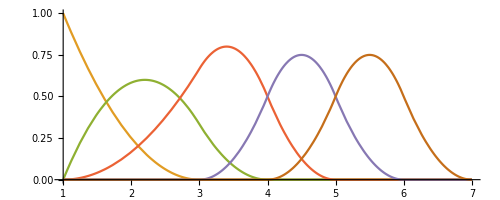

```mathematica
k=2;
BSpline=Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-3}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-3}]],{x,1,7},AspectRatio-> Automatic,PlotRange->All]
```

{t_3,t_5}={1,4}

3{1,1,1,1,3,4,5,6,7}0x | = (Piecewise[{{1/8 (27-27 x+9 x^2-x^3), 1≤x≤3}, {0, True}}])
3{1,1,1,1,3,4,5,6,7}1x | = (Piecewise[{{1/9 (64-48 x+12 x^2-x^3), 3≤x≤4}, {1/72 (-217+345 x-147 x^2+19 x^3), 1≤x<3}, {0, True}}])
3{1,1,1,1,3,4,5,6,7}2x | = (Piecewise[{{1/72 (49-111 x+75 x^2-13 x^3), 1≤x<3}, {1/8 (125-75 x+15 x^2-x^3), 4≤x≤5}, {1/72 (-923+861 x-249 x^2+23 x^3), 3≤x<4}, {0, True}}])
3{1,1,1,1,3,4,5,6,7}3x | = (Piecewise[{{1/24 (269-267 x+87 x^2-9 x^3), 3≤x<4}, {1/6 (216-108 x+18 x^2-x^3), 5≤x≤6}, {1/24 (-1+3 x-3 x^2+x^3), 1≤x<3}, {1/24 (-1011+693 x-153 x^2+11 x^3), 4≤x<5}, {0, True}}])
3{1,1,1,1,3,4,5,6,7}4x | = (Piecewise[{{1/6 (229-165 x+39 x^2-3 x^3), 4≤x<5}, {1/6 (343-147 x+21 x^2-x^3), 6≤x≤7}, {1/6 (-27+27 x-9 x^2+x^3), 3≤x<4}, {1/6 (-521+285 x-51 x^2+3 x^3), 5≤x<6}, {0, True}}])

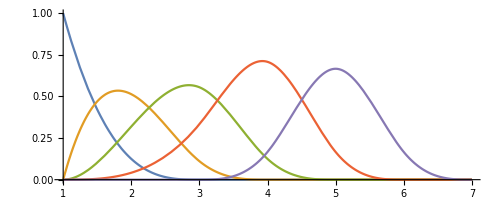

```mathematica
k=3;
Print[{Subscript[t, d],Subscript[t, e]},"=",{td,tmd}]
BSpline=Table[{TraditionalForm[BSplineBasis[{k,knots},i,x]],"="PiecewiseExpand[BSplineBasis[{k,knots},i,x]]},{i,0,m-4}]//TableForm
Plot[Evaluate[Table[BSplineBasis[{k,knots},i,x],{i,0,m-4}]],{x,1,7},AspectRatio-> Automatic,PlotRange->All]
```

```mathematica
Piece1=ParametricPlot[1/8 (27-27 x+9 x^2-x^3)b0+1/72 (-217+345 x-147 x^2+19 x^3)b1+1/72 (49-111 x+75 x^2-13 x^3)b2+1/24 (-1+3 x-3 x^2+x^3)b3,{x,1,3},Frame->True,Axes->False,PlotRange->All,PlotStyle->Green];
Piece2=ParametricPlot[1/9 (64-48 x+12 x^2-x^3)b1+1/72 (-923+861 x-249 x^2+23 x^3)b2+1/24 (269-267 x+87 x^2-9 x^3)b3+ 1/6 (-27+27 x-9 x^2+x^3)b4,{x,3,4},Frame->True,Axes->False,PlotRange->All,PlotStyle->Red];
```

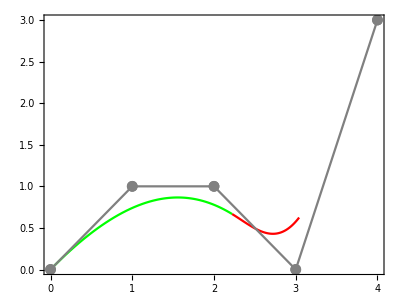

```mathematica
ctlpts=ListLinePlot[{b0,b1,b2,b3,b4},Mesh->Full, PlotStyle->Gray];
Show[{Piece1,Piece2,ctlpts},AspectRatio-> Automatic]
```

## 4) Built-in BSpline

#### Degree

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,1}};
Table[Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineDegree->d]}],{d,1,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Knot vectors

```mathematica
pts={{0,0},{0,2},{2,3},{4,0},{6,3},{8,2},{8,0}};
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineKnots->{0,1,2,3,4,5,6,7,8,9,10}]}]
```

-Graphics-

Using SplineKnots as automatic:

```mathematica
pts={{0,0},{0,2},{2,3},{4,0},{6,3},{8,2},{8,0}};
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineKnots->Automatic]}]
```

-Graphics-

Defining SplineKnots as automatic with d=3,n=6,, m=d+n+1=10:

```mathematica
pts={{0,0},{0,2},{2,3},{4,0},{6,3},{8,2},{8,0}};
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineKnots->{0,0,0,0,1,1,1,2,2,2,2}]}]
```

-Graphics-

### SplineClosed

```mathematica
pts={{0,0},{0,1},{1,1},{1,0}};
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts]}]
```

-Graphics-

Smoothly closed B-spline curve with the same control points:

```mathematica
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts, SplineClosed->True]}]
```

-Graphics-

### NURBS

Perfect circle using NURBS:

```mathematica
pts={{.5,0},{1,0},{1,1},{.5,1},{0,1},{0,0},{.5,0}};
w={1,.5,.5,1,.5,.5,1};
k={0,0,0,1/4,1/2,1/2,3/4,1,1,1};
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineWeights->w,SplineKnots->k]}]
```

-Graphics-

## Surfaces

## 1) Explicit Surfaces

```mathematica
ClearAll["Global`*"]
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},MeshStyle->Gray,Mesh->5]
```

-Graphics3D-

## 2) Implicit Surfaces

```mathematica
ClearAll["Global`*"]
iBall[x_,y_,z_]=x^2+y^2+z^2-10;
f1=ContourPlot3D[iBall[x,y,z]==0, {x,-6,6}, {y,-6,6}, {z,-6,6},MeshStyle->Gray,Mesh->3, ContourStyle->Opacity[0.5],ColorFunction->"Pastel"];
{iBall[1,1,2 √2],iBall[5,5,5],iBall[1,1,-1],iBall[1,1,-5]}
f2=Graphics3D[{PointSize[Large],Red,Point[{1,1,2 √2}]}];
f3=Graphics3D[{PointSize[Large],Magenta,Point[{5,5,5}]}];
f4=Graphics3D[{PointSize[Large],Green,Point[{1,1,-1}]}];
f5=Graphics3D[{PointSize[Large],Blue,Point[{1,5,-5}]}];
Show[{f1,f2,f3,f4,f5}]
```

{0,65,-7,17}

-Graphics3D-

## 3) Parametric Surface

### a) Bilinear Patch

```mathematica
ClearAll["Global`*"]
p00={1,1,2 √2};
p01={5,5,5};
p10={1,1,-1};
p11={1,5,-5};
fp00=Graphics3D[{PointSize[Large],Red,Point[p00]}];
fp01=Graphics3D[{PointSize[Large],Magenta,Point[p01]}];
fp10=Graphics3D[{PointSize[Large],Green,Point[p10]}];
fp11=Graphics3D[{PointSize[Large],Blue,Point[p11]}];
```

```mathematica
Bilinear[u_,v_]=(1-u)*(1-v)p00+(1-u)v p01+u(1-v)p10+u v p11
fB=ParametricPlot3D[Bilinear[u,v], {u,0,1},{v,0,1}];
Show[{fB,fp00,fp01,fp10,fp11}]
```

{(1-u) (1-v)+u (1-v)+5 (1-u) v+u v,(1-u) (1-v)+u (1-v)+5 (1-u) v+5 u v,2 √2 (1-u) (1-v)-u (1-v)+5 (1-u) v-5 u v}

-Graphics3D-

### b) Lofting

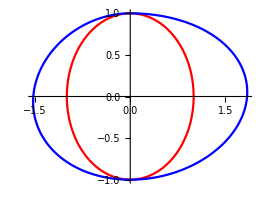

```mathematica
ClearAll["Global`*"]
C1[u_]:={Sin[u],Cos[u]}
C2[u_]:={(2-0.1 u) Sin[u],Cos[u]}
f1=Show[{ParametricPlot[C1[u],{u,0,2 π}, PlotStyle->Red],ParametricPlot[C2[u],{u,0,2 π},PlotStyle->Blue]}, PlotRange->All]
```

```mathematica
LoftedSurface[u_,v_]={(1-v)C2[u]+v C1[u],v}
f2=ParametricPlot3D[LoftedSurface[u,v],{u,0,2 π},{v,0,1},Mesh-> 4]
```

{{(2-0.1 u) (1-v) Sin[u]+v Sin[u],(1-v) Cos[u]+v Cos[u]},v}

-Graphics3D-

```mathematica
{{(2-0.1 u) (1-v) Sin[u]+v Sin[u],(1-v) Cos[u]+v Cos[u]},v}
```

{{(2-0.1 u) (1-v) Sin[u]+v Sin[u],(1-v) Cos[u]+v Cos[u]},v}

### c) Extrusion Surface

```mathematica
ClearAll["Global`*"]
C1[u_]:={Sin[u],Cos[u],0}
v={0,2,3};
f1=ParametricPlot3D[C1[u],{u,0,2 π}, PlotStyle->Blue];
f2=Graphics3D[{Blue,Arrow[Tube[{{0,0,0},v}]]}];
Show[{f1,f2},PlotRange->All]
```

-Graphics3D-

```mathematica
ExtrudeS[s_,t_]:=C1[s]+v t
f3=ParametricPlot3D[ExtrudeS[s,t],{s,0,2 π},{t,0,1}, AspectRatio->Automatic,PlotStyle->{ Specularity[White,50],Opacity[0.7]},Mesh->4];
Show[{f1,f2,f3},PlotRange->All]
```

-Graphics3D-

### d) Surface of Revolution

### x-axis

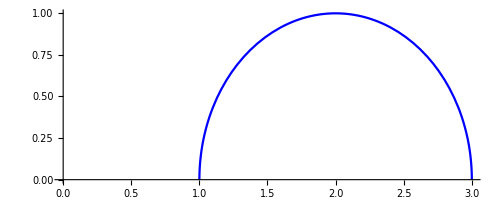

```mathematica
ClearAll["Global`*"]
C1[u_]:={2,0}+{Sin[u],Cos[u]}
ParametricPlot[C1[u],{u,-π/2,π/2}, PlotStyle->Blue, AxesOrigin->{0,0}]
m=Graphics3D[{PointSize[Large],Red,Point[{2,0,0}]}];
```

```mathematica
gx[u_]=C1[u][[1]];
gy[u_]=C1[u][[2]];
RevolveX[u_,θ_]:={gx[u],gy[u]Cos[θ],gy[u]Sin[θ]}
f1=ParametricPlot3D[RevolveX[u,θ],{u,-π/2,π/2},{θ,0,2 π}, AspectRatio->Automatic,Mesh-> 4,PlotStyle->{ Red,Specularity[White,50],Opacity[0.3]}];
Show[{f1,m}, PlotRange-> All, AxesLabel-> {x,y,z}]
```

-Graphics3D-

### y - axis

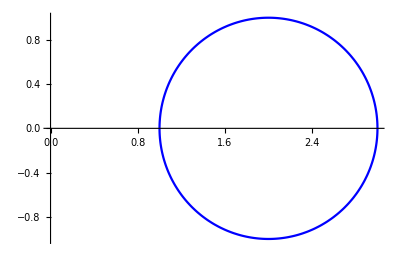

```mathematica
C1[u_]:={2,0}+{Sin[u],Cos[u]}
ParametricPlot[C1[u],{u,0,2π}, PlotStyle->Blue, AxesOrigin->{0,0}]
```

```mathematica
gx[u_]=C1[u][[1]];
gy[u_]=C1[u][[2]];
RevolveY[u_,θ_]:={gx[u]Cos[θ],gy[u],gx[u]Sin[θ]}
f2=ParametricPlot3D[RevolveY[u,θ],{u,0,2π},{θ,0,2 π}, AspectRatio->Automatic,Mesh-> 4,PlotStyle->{ White,Specularity[White,50],Opacity[0.3]}];
Show[{f1,f2,m}, PlotRange-> All, AxesLabel-> {x,y,z}]
```

-Graphics3D-

### z - axis

```mathematica
gx[u_]=C1[u][[1]];
gy[u_]=C1[u][[2]];
RevolveZ[u_,θ_]:={gx[u]Cos[θ],gx[u]Sin[θ],0}
f3=ParametricPlot3D[RevolveZ[u,θ],{u,0,2π},{θ,0,2 π}, AspectRatio->Automatic,Mesh-> 4,PlotStyle->{ Green,Opacity[0.1]}]
```

-Graphics3D-

```mathematica
Show[{f1,f2,f3,m}, PlotRange-> All, AxesLabel-> {x,y,z}]
```

-Graphics3D-

## 4) Tensor Product

### Bezier Surface

```mathematica
pts={{{0,0,0},{0,1,0},{0,2,0},{0,3,0}},{{1,0,0},{1,1,1},{1,2,1},{1,3,0}},
{{2,0,0},{2,1,2},{2,2,2},{2,3,0}},
{{3,0,0},{3,1,1},{3,2,1},{3,3,0}},{{4,0,0},{4,1,0},{4,2,0},{4,3,0}}};
f=BezierFunction[pts]
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts]}],
Graphics3D[{Gray,Line[pts],Line[Transpose[pts]]}],ParametricPlot3D[f[u,v],{u,0,1},{v,0,1},Mesh->True]]
```

BezierFunction[…]

-Graphics3D-

### B-Spline Surface

```mathematica
b=Graphics3D[BSplineSurface[pts,SplineDegree->2]];
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts],Gray,Line[pts],Line[Transpose[pts]]}],b]
```

-Graphics3D-

### NURBS

```mathematica
pts={{{0.5, 0, -0.5}, {0, 0, -0.5}, {0, 1, -0.5}, {0.5, 1, -0.5}, {1, 1, -0.5}, {1, 0, -0.5}, {0.5, 0, -0.5}}, 
 {{0.5, 0, 0.7}, {0, 0, 0.7}, {0, 1, 0.7}, {0.5, 1, 0.7}, {1, 1, 0.7}, {1, 0, 0.7}, {0.5, 0, 0.7}}, 
 {{0.5, 0, 0.9}, {0, 0, 0.9}, {0, 1, 1.5}, {0.5, 1, 1.5}, {1, 1, 1.5}, {1, 0, 0.9}, {0.5, 0, 0.9}}, 
 {{0.5, -0.1, 1}, {0, -0.1, 1}, {0, 0.5, 2}, {0.5, 0.5, 2}, {1, 0.5, 2}, {1, -0.1, 1}, {0.5, -0.1, 1}}, 
 {{0.5, -0.3, 1}, {0, -0.3, 1}, {0, -0.3, 2}, {0.5, -0.3, 2}, {1, -0.3, 2}, {1, -0.3, 1}, {0.5, -0.3, 1}}, 
 {{0.5, -1.5, 1}, {0, -1.5, 1}, {0, -1.5, 2}, {0.5, -1.5, 2}, {1, -1.5, 2}, {1, -1.5, 1}, {0.5, -1.5, 1}}};w={{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1},{1,.5,.5,1,.5,.5,1}};
uk={0,0,0,1/4,1/2,3/4,1,1,1};
vk={0,0,0,1/4,1/2,1/2,3/4,1,1,1};
```

```mathematica
pts//MatrixForm
```

((0.5
0
-0.5) | (0
0
-0.5) | (0
1
-0.5) | (0.5
1
-0.5) | (1
1
-0.5) | (1
0
-0.5) | (0.5
0
-0.5)
(0.5
0
0.7) | (0
0
0.7) | (0
1
0.7) | (0.5
1
0.7) | (1
1
0.7) | (1
0
0.7) | (0.5
0
0.7)
(0.5
0
0.9) | (0
0
0.9) | (0
1
1.5) | (0.5
1
1.5) | (1
1
1.5) | (1
0
0.9) | (0.5
0
0.9)
(0.5
-0.1
1) | (0
-0.1
1) | (0
0.5
2) | (0.5
0.5
2) | (1
0.5
2) | (1
-0.1
1) | (0.5
-0.1
1)
(0.5
-0.3
1) | (0
-0.3
1) | (0
-0.3
2) | (0.5
-0.3
2) | (1
-0.3
2) | (1
-0.3
1) | (0.5
-0.3
1)
(0.5
-1.5
1) | (0
-1.5
1) | (0
-1.5
2) | (0.5
-1.5
2) | (1
-1.5
2) | (1
-1.5
1) | (0.5
-1.5
1))

```mathematica
a=Graphics3D[{
FaceForm[Yellow,Blue],
BSplineSurface[pts,SplineKnots->{uk,vk},SplineDegree->2,SplineWeights->w,SplineClosed->{False,True}]},ViewPoint->{Right,Front},Boxed->False];
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts],Gray,Line[pts],Line[Transpose[pts]],
Text[Style["b00",Red,Italic,24],pts[[1,1]]],
Text[Style["b01",Red,Italic,24],pts[[1,2]]],
Text[Style["b02",Red,Italic,24],pts[[1,3]]],
Text[Style["b04",Red,Italic,24],pts[[1,4]]],
Text[Style["b05",Red,Italic,24],pts[[1,5]]],
Text[Style["b06",Red,Italic,24],pts[[1,6]]],
Text[Style["b07",Red,Italic,24],pts[[1,7]]],

(*Text[Style["b10",Red,Italic,24],pts[[2,1]]],
Text[Style["b11",Red,Italic,24],pts[[2,2]]],
Text[Style["b12",Red,Italic,24],pts[[2,3]]],
Text[Style["b14",Red,Italic,24],pts[[2,4]]],
Text[Style["b15",Red,Italic,24],pts[[2,5]]],
Text[Style["b16",Red,Italic,24],pts[[2,6]]],
Text[Style["b17",Red,Italic,24],pts[[2,7]]],*)

Text[Style["b50",Red,Italic,24],pts[[6,1]]],
Text[Style["b51",Red,Italic,24],pts[[6,2]]],
Text[Style["b52",Red,Italic,24],pts[[6,3]]],
Text[Style["b54",Red,Italic,24],pts[[6,4]]],
Text[Style["b55",Red,Italic,24],pts[[6,5]]],
Text[Style["b56",Red,Italic,24],pts[[6,6]]],
Text[Style["b57",Red,Italic,24],pts[[6,7]]]
}],a]
```

-Graphics3D-

```mathematica
Manipulate[
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts],Gray,Line[pts],Line[Transpose[pts]]}],Graphics3D[{
FaceForm[Yellow,Blue],
BSplineSurface[pts,SplineKnots->{uk,vk},SplineDegree->2,SplineWeights->{{1,a1,a2,a3,a4,.5,1},{1,a1,a2,a3,a4,.5,1},{1,a1,a2,a3,a4,.5,1},{1,a1,a2,a3,a4,.5,1},{1,a1,a2,a3,a4,.5,1},{1,a1,a2,a3,a4,.5,1}},SplineClosed->{False,True}]},ViewPoint->{Right,Front},Boxed->False]],{a1,0.1,1},{a2,0.1,1},{a3,0.1,1},{a4,0.1,1}]
```